# Entering data in real time into Mathematica 8

This may work exactly the same in Mathematica 7, but I did not test it.

## Insert Table/Matrix approach (probably the best way)

### Creating a table for data entry using the Insert Table/Matrix command

You can insert a empty grid or matrix from the Insert->Table/Matrix->New command in the menu.
You are given an option of Table or Matrix view.  I would choose Table for data entry, though it doesn’t matter.  Matrix view shows big matrix brackets on the outside of the table, which is nice for matrices, but would be unusual for a list of data.
You can also pick the number of rows and columns and also the appearance of gird lines separating the entries.
Give it a try.

I selected a Table with 2 columns and 4 rows

```mathematica
{{□, □}, {□, □}, {□, □}, {□, □}}
```

Give the table a name.  I set “data3” equal to this table and started entering in numbers.  It is easy to add rows and columns with keyboard shortcuts. 
Adding a row  < CTRL+ENTER >
Adding a column < CTRL+, >  (control+comma)
Deleting a row - highlight the row and press < Delete >
Deleting a column - highlight the column and press < Delete >

```mathematica
data3={{2, 3.1}, {3, 2.3}, {4, 2.8}, {5, 3.7}}
```

{{2,3.1},{3,2.3},{4,2.8},{5,3.7}}

The data is already in the format of an array and is ready to be plotted or analyzed.

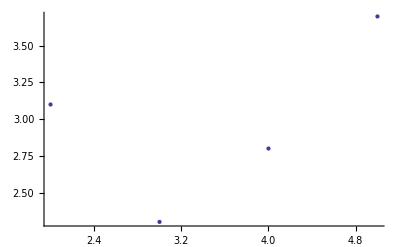

```mathematica
ListPlot[data3]
```

### Example for entry and plotting in real time

Nothing is new here other than the data entry and plot are combined on the same input section. Execute the input using  
< SHIFT + ENTER > whenever you want to produce the plot.

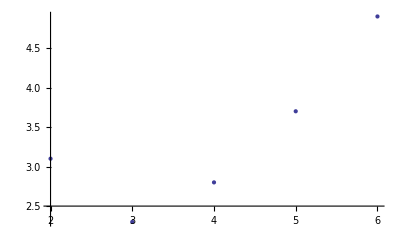

```mathematica
data3={{2, 3.1}, {3, 2.3}, {4, 2.8}, {5, 3.7}, {6, 4.9}, {□, □}};
ListPlot[data3]
```

## TableView - An undocumented function (it looks cool but is a little more cumbersome and may be buggy)

### Creating a spreadsheet-like table for entering data

First create a table by typing the command TableView[{nRows, nCols}].  This function is undocumented in Mathematica versions 7 and 8.

The table can be right clicked on to create and delete columns and rows and other operations.

```mathematica
TableView[{5,2}]
```

| 1 | 2
1 | □ | □
2 | □ | □
3 | □ | □
4 | □ | □
5 | □ | □

Copy the newly created table to a new input line.
I called my data set “data1” and set it equal to the empty table. Then I started entering in the values.

```mathematica
data1={{, 1, 2}, {1, 2.3, 123.4}, {2, 3, 203}, {3, 5, 293}, {4, 7, 283}, {5, 9.2, 150}, {6, □, □}, {7, □, □}};
```

Columns and rows can be added or removed by right clicking on the table.  
I have not found keyboard short commands for adding a row (which would be very useful for entering long data sets)

### Accessing the data from TableView[]

You will want the data in a Mathematica Array, but initially the data is stored as a more complicated TableView data type.  To just access the data you need to get just the first part of data1 by typing data1[[1]].   This gives you a Mathematica array of the data you just entered.

```mathematica
data1[[0]]
```

TableView

```mathematica
data2 = data1[[1]]
```

{{2.3,123.4},{3,203},{5,293},{7,283},{9.2,150},{Null,Null},{Null,Null}}

The "Null" entries in the matrix are because I left some of the elements in the array blank.

Now the data can be plotted or analyzed.

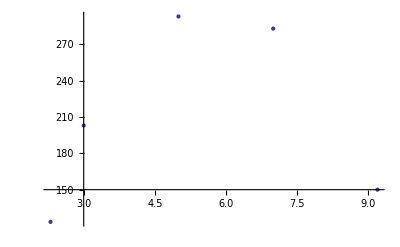

```mathematica
ListPlot[data2]
```